## Analysis with bayesian estimation

### Definitions;

```mathematica
Const;
```

```mathematica
(*Needs["CompiledFunctionTools`"];*)
$HistoryLength=0;
start=SessionTime[];
T2=2^8;nT2=2;
time=Range[nT2 T2];
```

#### Probability Function;

```mathematica
probabilityFunc=Compile[{{t,_Real,1},{δ1,_Real,0},{δ2,_Real,0},{A1,_Real,2},{A2,_Real,2},{B1,_Real,2},{B2,_Real,2}},0.5+(0.5-10^-15.)Sin[2.Sinc[δ1/2.](A1 Cos[t δ1]+B1 Sin[t δ1])+2. Sinc[δ2/2.](A2 Cos[t δ2]+B2 Sin[t δ2])],RuntimeAttributes->{Listable}];
probability=Function[{t,δ,Δ,Amp},probabilityFunc[t,δ-Δ/2,δ+Δ/2,Amp[[;;,1;;;;4]],Amp[[;;,2;;;;4]],Amp[[;;,3;;;;4]],Amp[[;;,4;;;;4]]]];
(*CompilePrint[probabilityFunc]*)
```

```mathematica
Meas=Function[{p0},Boole[MapThread[Less,{RandomReal[{0,1},Dimensions[p0]],p0},2]]];
```

#### Likelihood Funtion (BayesStep);

```mathematica
BayesStepFun=Compile[{{x,_Real,1},{p0,_Real,2}},Log2[(1-x)+(2x-1) p0],RuntimeAttributes->{Listable}];
(*CompilePrint[BayesStepFun];*)
BayesStep=Function[{x,p0},Total[BayesStepFun[x,p0],1]+T2 nT2];
```

#### Generating OU trajectories;

```mathematica
generateOUamplitudes=Function[{n},Transpose[RandomFunction[ARProcess[{Exp[-1/T2]},2/π(1-Exp[-2 1/T2])(π/10)^2],{0,nT2 T2-1} ,4 n]["ValueList"]]];
(*Block[{ou,prob,x,logL},
ou=generateOUamplitudes[2^10];
Print[ou//Dimensions];
prob=probability[time,2,3,ou];
x=Meas[prob];
Print[x//Dimensions];
logL=BayesStep[x[[;;,1]],prob];
Print[logL//Dimensions];
];*)
```

#### Calculate Log Likelihood of data over multiple OU trajectories;

```mathematica
SampleLogLikelihood=Function[{δ,Δ,numberOfSamples,Xdata},Block[{tab,JJ=Dimensions[Xdata][[2]]},
tab=Table[Block[{Xdatatemp=Xdata[[;;,jj]],tr,MyLikelihood1FreqSample,MyLikelihood2FreqSample},

If[Mod[jj+$KernelID,2^0]==0,SampleText[[$KernelID-SampleText[[-1]]]]={"Δ=",Δ T2/(2π),"Remaining steps ",NumberOfFreqLeft JJ-jj+1, " time to finish=",UnitConvert[Quantity[(SessionTime[]-start)/(Mod[NumberOfFreqLeft,2]JJ+jj-1+$MachineEpsilon)(NumberOfFreqLeft JJ-jj+1),"Seconds"],MixedRadix["Hours","Minutes","Seconds"]]}];
tr=generateOUamplitudes[numberOfSamples];
MyLikelihood1FreqSample=BayesStep[Xdatatemp,probability[time,δ,0 ,tr]];
MyLikelihood2FreqSample=BayesStep[Xdatatemp,probability[time,δ,Δ,tr]];
(*Are there two frequencies in the data?*)
{Mean[2^MyLikelihood1FreqSample]<Mean[2^MyLikelihood2FreqSample],Max[MyLikelihood1FreqSample]<Max[MyLikelihood2FreqSample],HistogramList[MyLikelihood1FreqSample],HistogramList[MyLikelihood2FreqSample],Log2[Mean[2^MyLikelihood1FreqSample]],Log2[Mean[2^MyLikelihood2FreqSample]],Max[MyLikelihood1FreqSample],Max[MyLikelihood2FreqSample]}
],{jj,1,JJ}];
<|"MeanEst"->Boole[tab[[;;,1]]],"MaxEst"->Boole[tab[[;;,2]]],"HistListOneFreqSample"->tab[[;;,3]],"HistListTwoFreqSample"->tab[[;;,4]]|>
]];
```

#### Run sampling iterations over measured X data;

```mathematica
IterationOverMeasurements=Function[{Δ,numberOfIterations,numberOfSamples},Block[{ou,δ=4Exp[3](2 π)/T2,x,Est,start=SessionTime[]},
NumberOfFreqLeft=2;(* one freq data *)
x=Meas[probability[time,δ,0,generateOUamplitudes[numberOfIterations]]];
Est=<|"OneFreqData"->SampleLogLikelihood[δ,Δ,numberOfSamples,x]|>;
NumberOfFreqLeft=1;(* two freq data *)
x=Meas[probability[time,δ,Δ,generateOUamplitudes[numberOfIterations]]];Est=Append[Est,"TwoFreqData"->SampleLogLikelihood[δ,Δ,numberOfSamples,x]]
]];
```

#### Plot Example;

```mathematica
(*Block[{nT2=20,time=Range[20 T2],cutoff=4,a,p,x,pl1,pl2,pl3,pl4,corr},
amp=Timing[generateOUamplitudes[1]];
Print[{"time=",amp[[1]],"Dimensions=[amp]",Dimensions[amp[[2]]]}];
amp=amp[[2]];
p=Timing[probability[time,6 (2 π)/T2,1 (2 π)/T2,amp]];
Print[{"time=",p[[1]],"Dimensions[ptemp]=",Dimensions[p[[2]]]}];
p=p[[2]];
x=Timing[Meas[p]];
Print[{"time=",x[[1]],"Dimensions[xtemp]=",Dimensions[x[[2]]]}];
x=x[[2]];
pl1=ListLinePlot[Transpose[amp],Filling->Axis,AxesLabel->{"t[τ]","OU Amplitudes"}];
pl2=ListLinePlot[Transpose[p],PlotRange->{0,1},Filling->0.5,AxesLabel->{"t[τ]","Probability for measurement outcome"}];
corr=Timing[(CovarianceFunction[x[[;;,1]],{cutoff T2}][[2;;]])(T2 nT2)/Range[T2 nT2,T2 (nT2-cutoff)+1,-1]];
Print[{"time=",corr[[1]],"Dimensions=[corrtemp]",Dimensions[corr[[2]]]}];
corr=corr[[2]];
pl3=ListLinePlot[corr,Filling->Axis,PlotRange->All,AxesLabel->{"Δt[τ]","Correlation Function"}];
pl4=ListLinePlot[Transpose[{Range[0,40-1]/cutoff,Abs[Fourier[corr][[;;40]]]}],Filling->Axis,GridLines->Automatic,PlotRange->All,AxesLabel->{"Frequency a.u.","Power Spectrum"}];
Print[GraphicsGrid[{{pl1,pl2},{pl3,pl4}},ImageSize->Full]];];*)
```

### Calculate mean and max of Likelihood;

```mathematica
Const Parameters
```

```mathematica
NumberOfMeasurementSets=2^10;
NumberOfSamples=2^15;
δvec=Range[0,1.5,0.05];
```

```mathematica
Launch Kernels and shared text for monitoring
```

```mathematica
(*If[$KernelCount<Length[δvec],Block[{},CloseKernels[];LaunchKernels[Length[δvec]]]];*)
CloseKernels[];LaunchKernels[16]
SampleText=Range[$KernelCount+1]0;
SetSharedVariable[SampleText];
SampleText[[-1]]=ParallelEvaluate[$KernelID][[1]]-1;
ParallelEvaluate[$KernelID]
Dynamic[SampleText[[;;-2]]//MatrixForm]
```

```mathematica
Run code
```

```mathematica
EstResults=Block[{start=SessionTime[]},ParallelTable[Block[{logL,est},
logL=IterationOverMeasurements[δvec[[δn]](2π)/T2,NumberOfMeasurementSets,NumberOfSamples]
],{δn,Length[δvec]}]];
SampleText={{"All done. Total time=",(SessionTime[]-start)/60^2,"Hours"},Null}
```

```mathematica
Extract results from structure and plot False Positive/Negative errors
```

```mathematica
FalsePositiveMean=EstResults[[;;,"OneFreqData","MeanEst"]]//Transpose//Mean;
FalsePositiveMax=EstResults[[;;,"OneFreqData","MaxEst"]]//Transpose//Mean;
FalseNegativeMean=1-EstResults[[;;,"TwoFreqData","MeanEst"]]//Transpose//Mean;
FalseNegativeMax=1-EstResults[[;;,"TwoFreqData","MaxEst"]]//Transpose//Mean;
mean={{FalseNegativeMean,FalsePositiveMean},{FalseNegativeMax,FalsePositiveMax}};
std=√((mean(1-mean))/NumberOfMeasurementSets);
Needs["ErrorBarPlots`"];
ErrorListPlot[{Transpose[{Transpose[{δvec,mean[[2,1]]}],Thread[ErrorBar[std[[2,1]]]]}],Transpose[{Transpose[{δvec,mean[[1,1]]}],Thread[ErrorBar[std[[1,1]]]]}],Transpose[{Transpose[{δvec,mean[[2,2]]}],Thread[ErrorBar[std[[2,2]]]]}],Transpose[{Transpose[{δvec,mean[[1,2]]}],Thread[ErrorBar[std[[1,2]]]]}]},PlotRange->{0,1},AxesLabel->{"beat-note","Probability"},PlotLegends->Placed[{"False Negative using Max[L]","False Negative using Mean[L]","False Positive using Max[L]","False Positive using Mean[L]"},{Scaled[{.05,.33}],{0,0}}],PlotLabel->"Are There Two Frequencies?",ImageSize->Large,GridLines->Automatic]
```

```mathematica
Plot average error
```

```mathematica
errorFromMean=(FalsePositiveMean+FalseNegativeMean)/2;
errorFromMax=(FalsePositiveMax+FalseNegativeMax)/2;
ListPlot[{Transpose[{δvec,errorFromMean}],Transpose[{δvec,errorFromMax}]}]
```

## Results presented in the article, and parameters used for the numerics

```mathematica
error rate from Mean[Likelihood] estimator;
```

```mathematica
errorFromMean={1013/2048,1053/2048,989/2048,1017/2048,1037/2048,507/1024,505/1024,973/2048,931/2048,933/2048,877/2048,215/512,105/256,179/512,737/2048,679/2048,637/2048,287/1024,539/2048,513/2048,15/64,455/2048,111/512,195/1024,171/1024,337/2048,37/256,275/2048,67/512,61/512,183/2048}
```

{1013/2048,1053/2048,989/2048,1017/2048,1037/2048,507/1024,505/1024,973/2048,931/2048,933/2048,877/2048,215/512,105/256,179/512,737/2048,679/2048,637/2048,287/1024,539/2048,513/2048,15/64,455/2048,111/512,195/1024,171/1024,337/2048,37/256,275/2048,67/512,61/512,183/2048}

```mathematica
error rate from Max[Likelihood] estimator;
```

```mathematica
errorFromMax={503/1024,525/1024,495/1024,1021/2048,1049/2048,1015/2048,1011/2048,487/1024,479/1024,233/512,445/1024,879/2048,211/512,183/512,743/2048,345/1024,325/1024,583/2048,17/64,519/2048,123/512,29/128,229/1024,395/2048,349/2048,87/512,75/512,141/1024,69/512,253/2048,95/1024}
```

{503/1024,525/1024,495/1024,1021/2048,1049/2048,1015/2048,1011/2048,487/1024,479/1024,233/512,445/1024,879/2048,211/512,183/512,743/2048,345/1024,325/1024,583/2048,17/64,519/2048,123/512,29/128,229/1024,395/2048,349/2048,87/512,75/512,141/1024,69/512,253/2048,95/1024}

```mathematica
frequncy differance  [(2π)/T2];
```

```mathematica
δvec=Range[0,1.5,0.05]
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5}

```mathematica
central frequncy [(2π)/T2]  (δj=δcenter±δvec/2);
```

```mathematica
4Exp[3]
```

4 ⅇ^3

```mathematica
number of data sets for statistics;
```

```mathematica
NumberOfMeasurementSets=2^10
```

1024

```mathematica
number of OU samples for "integration";
```

```mathematica
NumberOfSamples=2^15
```

32768

```mathematica
coherance time [τ];
```

```mathematica
T2=2^8
```

256

```mathematica
total time [T2];
```

```mathematica
nT2=2
```

2

```mathematica
plot;
```

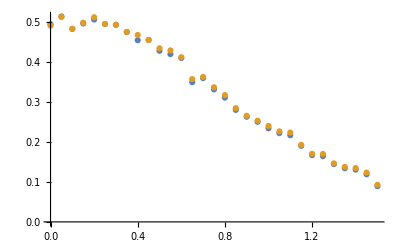

```mathematica
ListPlot[{Transpose[{δvec,errorFromMean}],Transpose[{δvec,errorFromMax}]}]
```